```mathematica
Quit[]
```

```mathematica
"FOR AJITH";
R=40 10^6;g = 8; ΔV0=g*0.35 10^-3;τ= 10 10^-3;τs= 1 10^-3;τs2= 4 10^-3;
Isyn[t_]=ΔV/R ⅇ t/τs ⅇ^(-t/τs)UnitStep[t];
Itotal[t_] = Isyn[t]+Isyn[t-2 10^-3]+Isyn[t-4 10^-3]+Isyn[t-6 10^-3];
Isyn2[t_]=ΔV/R ⅇ t/τs2 ⅇ^(-t/τs2)UnitStep[t];

res2=DSolve[{τ v'[t]==-v[t]+R Itotal[t],v[0]==0},v[t],t] //FullSimplify
Integrate[v[t]/.res2,{t,0,Infinity}]//FullSimplify
```

{{v[t]→2/81 ⅇ^(1-1000 t) ΔV (-5+4 ⅇ^2+13 ⅇ^4+22 ⅇ^6-4500 t-4500 ⅇ^2 t-4500 ⅇ^4 t-4500 ⅇ^6 t+(5-5 (1+ⅇ^(1/5)) ⅇ^(900 t)+4500 t+4 ⅇ^2 (-1+1125 t)) UnitStep[1/500-t]+(-5 ⅇ^(2/5+900 t)+ⅇ^4 (-13+4500 t)) UnitStep[1/250-t]-22 ⅇ^6 UnitStep[3/500-t]+4500 ⅇ^6 t UnitStep[3/500-t]-5 UnitStep[1/500-t,t]-4500 t UnitStep[1/500-t,t]+5 ⅇ^(900 t) ((1+ⅇ^(1/5)) (1+ⅇ^(2/5))-ⅇ^(3/5) UnitStep[3/500-t]+UnitStep[1/500-t,t]))}}

{(ⅇ ΔV)/250}

{{v→InterpolatingFunction[{{0., 0.05}}, <>]}}

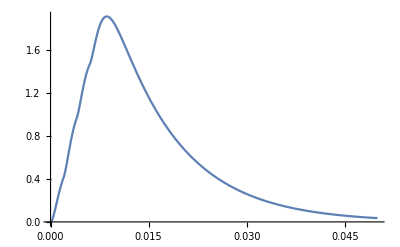

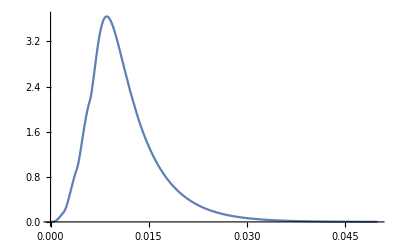

{3.50553×10^-8}

```mathematica
Numerical integration;

Isyn[t_]=ΔV0/R ⅇ t/τs ⅇ^(-t/τs)UnitStep[t];
Itotal[t_] = Isyn[t]+Isyn[t-2 10^-3]+Isyn[t-4 10^-3]+Isyn[t-6 10^-3];
res2=NDSolve[{τ v'[t]==-v[t]+R Itotal[t] ,v[0]==0},v,{t,0,0.05}] 
Plot[1 10^3 v[t]/.res2,{t,0,0.05}]
Plot[1 10^6 v[t]^2/.res2,{t,0,0.05}]
NIntegrate[v[t]^2/.res2,{t,0,0.05}]
```

```mathematica
Integrate[v[t]^2/.res2,{t,0,Infinity}]
```

$Aborted

```mathematica
2 10^-3/R*1 10^12
```

50

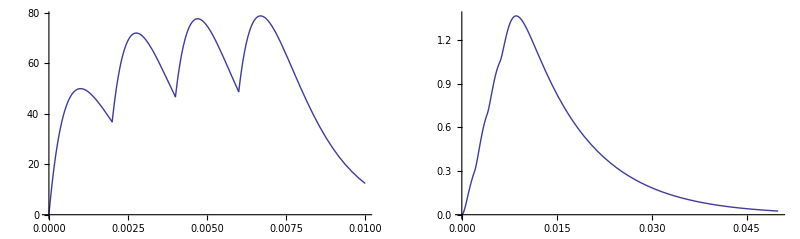

```mathematica
pl1=Plot[1 10^12 Itotal[t]/.res2/.{ΔV->ΔV0},{t,0,0.01},PlotRange->Full];
pl2=Plot[1 10^3 v[t]/.res2/.{ΔV->ΔV0},{t,0,0.05},PlotRange->Full];
GraphicsRow[{pl1,pl2},ImageSize->800]
```